Import the AtomicDensityMatrix package.  Available at http://rochesterscientific.com/ADM/.

```mathematica
<<AtomicDensityMatrix`
```

### Functions

Generate a table of the coupling coefficients between, and energy levels of, the ground (gs) and excited (es) magnetic sublevels in a field of strength B (where B is twice the Zeeman splitting of the ground F=1, mF=+/-1 subevels from the F=1,mF=0 sublevel.

```mathematica
CoeficientTable[gs_,es_,B_]:=Module[{d,h},
d=√2Table[WignerEckart[g,{Dipole,1,M[g]-M[e]},e]/.ReducedME[1,{Dipole,1},2]->1,{g,gs},{e,es}];
h=Hamiltonian[es,MagneticField->{0,0,B}]/.BohrMagneton->1;
TableForm[d.Eigenvectors[h]ᵀ,TableHeadings->Table[Table[{F[i],M[i]},{i,states}],{states,{gs,es}}]]]

EnergyLevels[s_,B_]:=Module[{h},
h=Hamiltonian[s,MagneticField->{0,0,B}]/.BohrMagneton->1;
TableForm[Eigenvalues[h],TableHeadings->{Table[{F[i],M[i]},{i,s}]}]
]
```

These functions track the changing energy states and coupling values (as they are not returned in a consistent order from ADM).

```mathematica
SourceTargetCostMatrix[pointsA_,pointsB_,costFunction_:EuclideanDistance]:=Module[{lA=Length[pointsA],lB=Length[pointsB]},ArrayFlatten@{{0,ConstantArray[1,{1,lA}],ConstantArray[0,{1,lB}],0},{ConstantArray[0,{lA,1}],ConstantArray[0,{lA,lA}],Outer[costFunction,pointsA,pointsB,1],ConstantArray[0,{lA,1}]},{ConstantArray[0,{lB,1}],ConstantArray[0,{lB,lA}],ConstantArray[0,{lB,lB}],ConstantArray[1,{lB,1}]},{0,ConstantArray[0,{1,lA}],ConstantArray[0,{1,lB}],0}}]

ReorderEigenvectors[oldVecs_,newVecs_]:=Module[{costMatrix,assignments,idx},
costMatrix=SourceTargetCostMatrix[newVecs,oldVecs,-Abs[Dot[#1,#2]]&];
assignments=List@@@Cases[FindMinimumCostFlow[costMatrix,1,Length[costMatrix],"EdgeList"],x_->y_/;x≠1&&y≠Length[costMatrix]];
assignments=Transpose[{assignments[[;;,1]]-1,assignments[[;;,2]]-1-Length[oldVecs]}];
idx=SortBy[assignments,Last][[;;,1]];
newVecs[[idx]]
]
```

```mathematica
FollowOrderEigenvectors[eigenvectorTimeseries_]:=FoldList[ReorderEigenvectors[#1,#2]&,eigenvectorTimeseries]
```

```mathematica
CoefficientSeries[gs_,es_,Bs_]:=Module[{d, eigenvectorSeries},
d=Table[If[M[g]-M[e]==-1||M[g]-M[e]==0||M[g]-M[e]==1, -1^{1+3/2+J[g]+F[e]+F[g]+M[g]}*Sqrt[(2F[g]+1)*(2F[e]+1)*(2J[g]+1)]*ThreeJSymbol[{F[e],M[e]},{1,M[g]-M[e]},{F[g],-M[g]}]*SixJSymbol[{J[g], J[e],1},{F[e],F[g],3/2}],{0}],{g,gs},{e,es}][[All,All,1]];
eigenvectorSeries=FollowOrderEigenvectors@Table[
Eigenvectors[
Hamiltonian[es,MagneticField->{0,0,B}]/.BohrMagneton->1
],
{B,Bs}
];
Transpose[{Bs,d.#ᵀ&/@eigenvectorSeries}]];
```

Calculate dipole matrix elements with correct signs in accordance to Steck.

```mathematica
DTable[gs_,es_]:=Table[If[M[g]-M[e]==-1||M[g]-M[e]==0||M[g]-M[e]==1, -1^{2*F[e]+J[g]+3/2+M[g]}*Sqrt[(2F[g]+1)*(2F[e]+1)*(2J[g]+1)]*ThreeJSymbol[{F[e],M[e]},{1,M[g]-M[e]},{F[g],-M[g]}]*SixJSymbol[{J[g], J[e],1},{F[e],F[g],3/2}],{0}],{g,gs},{e,es}][[All,All,1]];
```

### Calculate coefficient table

Set up the F=1 (gs1), F=2 (gs2) and F’=1,2 (es) levels of 87Rb.

```mathematica
gs1=SelectStates[Sublevels[
AtomicState[1,L->0,S->1/2,J->1/2,NuclearSpin->3/2,Energy->0,HyperfineA->3417.341305452155,HyperfineB->0]],F==1];
gs2=SelectStates[Sublevels[
AtomicState[1,L->0,S->1/2,J->1/2,NuclearSpin->3/2,Energy->0,HyperfineA->3417.341305452155,HyperfineB->0]],F==2];
es=Sublevels[
AtomicState[2,L->1,S->1/2,J->1/2,NuclearSpin->3/2,Energy->510.410,HyperfineA->408.328,HyperfineB->0]];
(*d=√2Table[WignerEckart[g,{Dipole,1,M[g]-M[e]},e]/.ReducedME[1,{Dipole,1},2]->1,{g,gs},{e,es}];*)
```

```mathematica
Bs=Table[i,{i,0,20,0.1}];
```

```mathematica
{coeffSeriesF1MM,coeffSeriesF1M, coeffSeriesF1,coeffSeriesF1P,coeffSeriesF1PP} =CoefficientSeries[gs1,SelectStates[es,M==#],Bs]&/@{-2,-1,0,1,2};
```

```mathematica
{coeffSeriesF2MM,coeffSeriesF2M, coeffSeriesF2,coeffSeriesF2P,coeffSeriesF2PP} =CoefficientSeries[gs2,SelectStates[es,M==#],Bs]&/@{-2,-1,0,1,2};
```

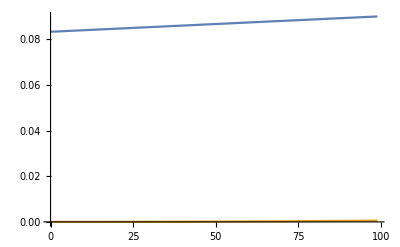

```mathematica
ListPlot[Table[{B,(CoeficientTable[gs1,SelectStates[es,M==0],B][[1,i,2]])^2},{i,2},{B,0,100,3}],Joined->True]
```

### Save parameters to file

#### Calculate parameters

```mathematica
ΔZground=0;
B=2*ΔZground;

Beff =Nearest[Bs,B][[1]];
```

```mathematica
{coeffTableF1MM,coeffTableF1M, coeffTableF1,coeffTableF1P,coeffTableF1PP} =(Function[coeffSeries,Select[coeffSeries, #[[1]]==B&][[1,2]]])/@{coeffSeriesF1MM,coeffSeriesF1M, coeffSeriesF1,coeffSeriesF1P,coeffSeriesF1PP} ;
{coeffTableF2MM,coeffTableF2M, coeffTableF2,coeffTableF2P,coeffTableF2PP} =(Function[coeffSeries,Select[coeffSeries, #[[1]]==B&][[1,2]]])/@{coeffSeriesF2MM,coeffSeriesF2M, coeffSeriesF2,coeffSeriesF2P,coeffSeriesF2PP} ;
```

```mathematica
tableFormat[table_]:=MapAt[If[#==0,#,Sign[#]DisplayForm@SqrtBox[Evaluate@Rationalize[#^2]]]&,table,{All,All}]

Grid[{
{TableForm[tableFormat@coeffTableF1PP,TableHeadings->Table[Table[{F[i],M[i]},{i,states}],{states,{gs1,SelectStates[es,M==2]}}]],
TableForm[tableFormat@coeffTableF1MM,TableHeadings->Table[Table[{F[i],M[i]},{i,states}],{states,{gs1,SelectStates[es,M==-2]}}]]},
{TableForm[tableFormat@coeffTableF1P,TableHeadings->Table[Table[{F[i],M[i]},{i,states}],{states,{gs1,SelectStates[es,M==1]}}]],
TableForm[tableFormat@coeffTableF1M,TableHeadings->Table[Table[{F[i],M[i]},{i,states}],{states,{gs1,SelectStates[es,M==-1]}}]]},
{TableForm[tableFormat@coeffTableF1,TableHeadings->Table[Table[{F[i],M[i]},{i,states}],{states,{gs1,SelectStates[es,M==0]}}]],SpanFromLeft}
}]

Grid[{
{TableForm[tableFormat@coeffTableF2PP,TableHeadings->Table[Table[{F[i],M[i]},{i,states}],{states,{gs2,SelectStates[es,M==2]}}]],
TableForm[tableFormat@coeffTableF2MM,TableHeadings->Table[Table[{F[i],M[i]},{i,states}],{states,{gs2,SelectStates[es,M==-2]}}]]},
{TableForm[tableFormat@coeffTableF2P,TableHeadings->Table[Table[{F[i],M[i]},{i,states}],{states,{gs2,SelectStates[es,M==1]}}]],
TableForm[tableFormat@coeffTableF2M,TableHeadings->Table[Table[{F[i],M[i]},{i,states}],{states,{gs2,SelectStates[es,M==-1]}}]]},
{TableForm[tableFormat@coeffTableF2,TableHeadings->Table[Table[{F[i],M[i]},{i,states}],{states,{gs2,SelectStates[es,M==0]}}]],SpanFromLeft}
}]
```

| {2,2}
{1,1} | -√(1/2)
{1,0} | 0.
{1,-1} | 0. |  | {2,-2}
{1,1} | 0.
{1,0} | 0.
{1,-1} | -√(1/2)
 | {2,1} | {1,1}
{1,1} | -√(1/4) | √(1/12)
{1,0} | -√(1/4) | -√(1/12)
{1,-1} | 0. | 0. |  | {2,-1} | {1,-1}
{1,1} | 0. | 0.
{1,0} | -√(1/4) | √(1/12)
{1,-1} | -√(1/4) | -√(1/12)
 | {2,0} | {1,0}
{1,1} | √(1/12) | -√(1/12)
{1,0} | √(1/3) | 0.
{1,-1} | √(1/12) | √(1/12) |

| {2,2}
{2,2} | -√(1/3)
{2,1} | √(1/6)
{2,0} | 0.
{2,-1} | 0.
{2,-2} | 0. |  | {2,-2}
{2,2} | 0.
{2,1} | 0.
{2,0} | 0.
{2,-1} | -√(1/6)
{2,-2} | √(1/3)
 | {2,1} | {1,1}
{2,2} | -√(1/6) | √(1/2)
{2,1} | -√(1/12) | -√(1/4)
{2,0} | √(1/4) | √(1/12)
{2,-1} | 0. | 0.
{2,-2} | 0. | 0. |  | {2,-1} | {1,-1}
{2,2} | 0. | 0.
{2,1} | 0. | 0.
{2,0} | -√(1/4) | √(1/12)
{2,-1} | √(1/12) | -√(1/4)
{2,-2} | √(1/6) | √(1/2)
 | {2,0} | {1,0}
{2,2} | 0. | 0.
{2,1} | √(1/4) | -√(1/4)
{2,0} | 0. | √(1/3)
{2,-1} | -√(1/4) | -√(1/4)
{2,-2} | 0. | 0. |

#### Assign parameters to variables

```mathematica
(* Assign Subscript[A, ij] values |F=1,mF> -> |F={1,2},mF> *)
{na,na,CGg1Mx2MM}=coeffTableF1MM;
{{na,na},{CGg1x2M,CGg1x1M},{CGg1Mx2M,CGg1Mx1M}}=coeffTableF1M;
{{CGg1Px2,CGg1Px1},{CGg1x2,CGg1x1},{CGg1Mx2,CGg1Mx1}}=coeffTableF1;
{{CGg1Px2P,CGg1Px1P},{CGg1x2P,CGg1x1P},{na,na}}=coeffTableF1P;
{CGg1Px2PP,na,na}=coeffTableF1PP;
```

```mathematica
(* Assign Subscript[A, ij] values |F=2,mF> -> |F={1,2},mF> *)

{na,na,na,CGg2Mx2MM, CGg2MMx2MM}=  coeffTableF2MM;
{{na,na},{na,na},{CGg2x2M,CGg2x1M},{CGg2Mx2M,CGg2Mx1M},{CGg2MMx2M,CGg2MMx1M}}=coeffTableF2M;
{{na,na},{CGg2Px2,CGg2Px1},{CGg2x2,CGg2x1},{CGg2Mx2,CGg2Mx1},{na,na}}=coeffTableF2;
{{CGg2PPx2P,CGg2PPx1P},{CGg2Px2P,CGg2Px1P},{CGg2x2P,CGg2x1P},{na,na},{na,na}}=coeffTableF2P;
{CGg2PPx2PP,CGg2Px2PP,na,na,na}=coeffTableF2PP;
```

```mathematica
(* Assign ΔZi values *)
energyTableZero=EnergyLevels[SelectStates[es,M==0],0]
```

{2,0} | 816.656
{1,0} | 0.

```mathematica
{energyTableMM,energyTableM, energyTable,energyTableP,energyTablePP} =EnergyLevels[SelectStates[es,M==#],B]&/@{-2,-1,0,1,2}
```

{{2,-2} | 816.656,{2,-1} | 816.656
{1,-1} | 0.,{2,0} | 816.656
{1,0} | 0.,{2,1} | 816.656
{1,1} | 0.,{2,2} | 816.656}

```mathematica
ΔZx2MM=energyTableMM[[1]]-energyTableZero[[1]][[1]]
```

{0.}

```mathematica
{ ΔZx2M,ΔZx1M}=energyTableM[[1]]-energyTableZero[[1]][[;;2]] ;
{ΔZx2,ΔZx1}=energyTable[[1]]-energyTableZero[[1]];
{ ΔZx2P,ΔZx1P}=energyTableP[[1]]-energyTableZero[[1]][[;;2]] ;
 ΔZx2PP=energyTablePP[[1]]-energyTableZero[[1]][[1]] ;
```

```mathematica
ΔEx1 = #[[2]]-#[[1]]&@energyTableZero[[1]]
ΔZ = EnergyLevels[SelectStates[gs2,M==1],B][[1,1]] - EnergyLevels[SelectStates[gs2,M==1],0][[1,1]]
```

-816.656

0.

#### Save to file

```mathematica
CGsg1=Transpose[{
{"CGg1Mx2MM",
"CGg1x2M","CGg1x1M","CGg1Mx2M","CGg1Mx1M",
"CGg1Px2","CGg1Px1","CGg1x2","CGg1x1","CGg1Mx2","CGg1Mx1",
"CGg1Px2P","CGg1Px1P","CGg1x2P","CGg1x1P",
"CGg1Px2PP"},
{Flatten[CGg1Mx2MM],
CGg1x2M,CGg1x1M,CGg1Mx2M,CGg1Mx1M,
CGg1Px2,CGg1Px1,CGg1x2,CGg1x1,CGg1Mx2,CGg1Mx1,
CGg1Px2P,CGg1Px1P,CGg1x2P,CGg1x1P,
CGg1Px2PP}
}];
CGsg2=Transpose[{
{"CGg2Mx2MM","CGg2MMx2MM",
"CGg2x2M","CGg2x1M","CGg2Mx2M","CGg2Mx1M","CGg2MMx2M","CGg2MMx1M",
"CGg2Px2","CGg2Px1","CGg2x2","CGg2x1","CGg2Mx2","CGg2Mx1",
"CGg2PPx2P","CGg2PPx1P","CGg2Px2P","CGg2Px1P","CGg2x2P","CGg2x1P",
"CGg2PPx2PP","CGg2Px2PP"},
{
CGg2Mx2MM,CGg2MMx2MM,
CGg2x2M,CGg2x1M,CGg2Mx2M,CGg2Mx1M,CGg2MMx2M,CGg2MMx1M,
CGg2Px2,CGg2Px1,CGg2x2,CGg2x1,CGg2Mx2,CGg2Mx1,
CGg2PPx2P,CGg2PPx1P,CGg2Px2P,CGg2Px1P,CGg2x2P,CGg2x1P,
CGg2PPx2PP,CGg2Px2PP
}
}];

deltas=Transpose[{{"deltaZ","deltaEx1",
"deltaZx2MM",
"deltaZx2M","deltaZx1M",
"deltaZx2","deltaZx1",
"deltaZx2P","deltaZx1P",
"deltaZx2PP"
},
{ΔZ,ΔEx1,
ΔZx2MM,
ΔZx2M,ΔZx1M,
ΔZx2,ΔZx1,
ΔZx2P,ΔZx1P,
ΔZx2PP}
}];
data = {CGsg1,CGsg2,deltas};
data//TableForm
```

CGg1Mx2MM
-0.707107 | CGg1x2M
-0.5 | CGg1x1M
0.288675 | CGg1Mx2M
-0.5 | CGg1Mx1M
-0.288675 | CGg1Px2
0.288675 | CGg1Px1
-0.288675 | CGg1x2
0.57735 | CGg1x1
0. | CGg1Mx2
0.288675 | CGg1Mx1
0.288675 | CGg1Px2P
-0.5 | CGg1Px1P
0.288675 | CGg1x2P
-0.5 | CGg1x1P
-0.288675 | CGg1Px2PP
-0.707107 |  |  |  |  |  | 
CGg2Mx2MM
-0.408248 | CGg2MMx2MM
0.57735 | CGg2x2M
-0.5 | CGg2x1M
0.288675 | CGg2Mx2M
0.288675 | CGg2Mx1M
-0.5 | CGg2MMx2M
0.408248 | CGg2MMx1M
0.707107 | CGg2Px2
0.5 | CGg2Px1
-0.5 | CGg2x2
0. | CGg2x1
0.57735 | CGg2Mx2
-0.5 | CGg2Mx1
-0.5 | CGg2PPx2P
-0.408248 | CGg2PPx1P
0.707107 | CGg2Px2P
-0.288675 | CGg2Px1P
-0.5 | CGg2x2P
0.5 | CGg2x1P
0.288675 | CGg2PPx2PP
-0.57735 | CGg2Px2PP
0.408248
deltaZ
0. | deltaEx1
-816.656 | deltaZx2MM
0. | deltaZx2M
0. | deltaZx1M
0. | deltaZx2
0. | deltaZx1
0. | deltaZx2P
0. | deltaZx1P
0. | deltaZx2PP
0. |  |  |  |  |  |  |  |  |  |  |  |

```mathematica
(*Export["/Users/ernst/Desktop/d1_params/exp_params_D1_"<>StringReplace[ToString[Abs@ΔZ],"."->"p"]<>"MHz.csv",Flatten[data,1], "TextDelimiters"-> None]*)
```